```mathematica
Homework 4
```

```mathematica
John Knowles
```

```mathematica
{{Do, While, Increment(++), Input, For, +=,*=}, {Nest, NestList, NestWhile, NestWhileList, FixedPointList, LengthWhile}, {TakeWhile, Fold, FoldList, Accumulate, Sequence, Rule}}
```

## 1. Problem 7.1

```mathematica
sP=Select[Range[30],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
Do[Print[n," -> ",Length[Intersection[Range[n+1,2n-1],sP]]],{n,1,15}]
```

1 -> 0

2 -> 1

3 -> 1

4 -> 2

5 -> 1

6 -> 2

7 -> 2

8 -> 2

9 -> 3

10 -> 4

11 -> 3

12 -> 4

13 -> 3

14 -> 3

15 -> 4

## 2. Problem 7.2

```mathematica
M={};
Do[M=Union[M,Select[Range[0,500],(PrimeQ[#^2+#+i]==False)&,1]],{i,0,10000}];M
```

{0,1,2,3,4,5,6,7,10,16,40}

```mathematica
Do[M=(M∪Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1]),{i,1,10000}];M
```

{0,1,2,3,4,5,6,7,10,16,40}

```mathematica
A={};
Do[AppendTo[A,Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1][[1]]],{i,1,10000}];A
```

{0,1,2,0,4,0,1,0,0,0,10,0,1,0,0,0,16,0,1,0,0,0,1,0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0,0,40,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,2,0,1,0,0,0,0,0,1,0,0,0,2,0,1,0,0,0,0,0,1,0,9840,0,0,1,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Counts[A]
```

<|0→8771,1→1024,2→150,4→11,10→1,16→1,40→1,3→31,5→7,7→1,6→2|>

```mathematica
B={};
Reap[
Do[AppendTo[B,If[Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1][[1]]==40,Sow[i];(*Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1][[1]] -- Arbitrary*),(*Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1][[1]] -- neither T||F*)]],{i,1,10000}]][[2,1,1]]
```

41

## 3. Exercise 7.1

```mathematica
B={};
Reap[
Do[AppendTo[B,If[MemberQ[{10,12,16,40},Select[Range[0,500],(PrimeQ[#^2+#+i]==False&),1][[1]]],Sow[i];]],{i,1,10000}]][[2,1]]
```

{11,17,41}

## 4. Problem 7.3

```mathematica
Do[If[LCM[i,5432-i]==223020,Print[i," ",5432-i]],{i,1,2718}]
```

1652 3780

## 5. Problem 7.4

```mathematica
n=111;
While[!PrimeQ[n],n=10n+1];Print[n]
```

1111111111111111111

## 6. Problem 7.5

```mathematica
m=1;
While[Mod[529^3+132^3m,262417]≠0,m++];m
```

1984

## 7. Problem 7.6

```mathematica
n=Input["Choose a number: "]
While[!PrimeQ[n],n--];Print[n]
```

543

541

## 8. Problem 7.7

```mathematica
i=1; n=Input["Choose a number: "]; A={};
While[Prime[i]≤n,AppendTo[A,Prime[i]];i++];A
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317}

## 9. Exercise 7.2

```mathematica
m = n=99999;i=1;
While[MemberQ[IntegerDigits[m],9],m=n*i++];Print[i, " ",m]
```

11113 1111188888

## 10. Problem 7.8

```mathematica
A={};Do[i=0;
While[Mod[(5n)!/(n!)^5,5^i]==0,AppendTo[A,{n,i}];i++],{n,1,200}]
A;
Last/@A;
Max[Last/@A]
```

12

```mathematica
Select[A,#[[2]]==12&]
```

{{124,12}}

```mathematica
B=Reap[Do[i=0;While[Mod[(5n)!/(n!)^5,5^i]==0,Sow[{n,i}];i++],{n,1,200}]][[2,1]]
```

```mathematica
{a,b}=Select[B,#[[2]]==Max[Last/@B]&][[1]]
```

{124,12}

```mathematica
Divisible[(5*a)!/(a!)^5,5^b]
```

True

## 11. Problem 7.9

```mathematica
For[i=1;sum=0,i<11,i++,sum+=i/(i+i+1)];sum
```

64157087/14549535

```mathematica
Sum[i/(2i+1),{i,1,10}]
```

64157087/14549535

```mathematica
Plus@@(#/(2#+1)&/@Range[10])
```

64157087/14549535

## 12. Problem 7.10

```mathematica
n=Input["Enter a number to check if it is palindromic: "];nDecomp = IntegerDigits[n]; Print["Your number was: ",FromDigits[nDecomp]]
If[nDecomp==Reverse[nDecomp],Print["It is indeed, palindromic."],Print["This isn't palindromic...Let's try adding both..."]]
Reap[While[nDecomp≠Reverse[nDecomp],n=n+FromDigits[Reverse[nDecomp]];nDecomp=IntegerDigits[n]; Sow[FromDigits[nDecomp]]]][[2,1]]
Print["Your final palindromic number: ", FromDigits[nDecomp]]
```

Your number was: 89

This isn't palindromic...Let's try adding both...

{187,968,1837,9218,17347,91718,173437,907808,1716517,8872688,17735476,85189247,159487405,664272356,1317544822,3602001953,7193004016,13297007933,47267087164,93445163438,176881317877,955594506548,1801200002107,8813200023188}

Your final palindromic number: 8813200023188

## 13. Problem 7.11

```mathematica
Do[Do[If[Sqrt[a^2+b^2]∈Integers,Print[a, " ",b]],{b,a,10}],{a,1,10}]
```

3 4

6 8

## 14. Exercise 7.3

```mathematica
Select[Select[Flatten[Table[{i,j},{i,0,10},{j,i,10}],1],(Reverse[IntegerDigits[#[[1]]]]==IntegerDigits[#[[2]]^2])&], (Sqrt[#[[1]]^2+#[[2]]^2]∈Integers&)]
```

{{0,0}}

## 15. Exercise 7.4

```mathematica
p=Input["Pick an odd prime number: (3, 5, 7, ,11, 13,...etc)"];
Do[Do[If[Sqrt[r^2-q^2]==p,Print[Superscript[p,2]," + ",Superscript[q,2]," = ", Superscript[r,2]]],{r,q,100}],{q,1,100}]
```

5^2 + 12^2 = 13^2

## 16. Exercise 7.5

```mathematica
f[x_]:=1/(1+x);
1+Nest[f,x,10]
Solve[1+Nest[f,x,10]==x,x]
NSolve[x==1+Nest[f,x,10],x]
```

1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

{{x→-12/(√55)},{x→12/(√55)}}

{{x→1.61808},{x→-1.61808}}

## 17. Exercise 7.6

```mathematica
f[x_]:=Nest[Sqrt[2+#]&,Sqrt[2],x]
N[Table[Product[f[n]/2,{n,0,k}],{k,1,25}]][[-1]]==2./Pi
```

True

## 18. Problem 7.12

```mathematica
(*break digit apart, square them, add them, repeat until process reaches 1 *)
Select[Range[100],NestWhile[Plus@@(IntegerDigits[#]^2)&,#,(!#==4)&&(!#==1)&]==1&]
```

{1,7,10,13,19,23,28,31,32,44,49,68,70,79,82,86,91,94,97,100}

```mathematica
Plus@@(IntegerDigits[7]^2)
Plus@@(IntegerDigits[49]^2)
Plus@@(IntegerDigits[97]^2)
Plus@@(IntegerDigits[130]^2)
Plus@@(IntegerDigits[10]^2)
```

49

97

130

10

1

## 19. Problem 7.13

```mathematica
Drop[FixedPointList[Quotient[#,10]&,53713453],-2](*LengthWhile & TakeWhile are similar*)
```

{53713453,5371345,537134,53713,5371,537,53,5}

```mathematica
pP[x_]:=And@@PrimeQ[Drop[FixedPointList[Quotient[#,10]&,x],-2]]
Select[Range[0,9999],pP]
Select[Range[3733*10+1,3733*10+9,2],PrimeQ]
pList={2,3,5,7}
Select[Flatten[Range[10#+1,10#+9,2]&[pList]],PrimeQ]
```

{0,2,3,5,7,23,29,31,37,53,59,71,73,79,233,239,293,311,313,317,373,379,593,599,719,733,739,797,2333,2339,2393,2399,2939,3119,3137,3733,3739,3793,3797,5939,7193,7331,7333,7393}

{37337,37339}

{2,3,5,7}

{23,29,31,37,53,59,71,73,79}

```mathematica
pList={2,3,5,7};
While[!pList=={},Print[pList];pList=Select[Flatten[Range[10#+1,10#+9,2]&[pList]],PrimeQ]
]
```

{2,3,5,7}

{23,29,31,37,53,59,71,73,79}

{233,239,293,311,313,317,373,379,593,599,719,733,739,797}

{2333,2339,2393,2399,2939,3119,3137,3733,3739,3793,3797,5939,7193,7331,7333,7393}

{23333,23339,23399,23993,29399,31193,31379,37337,37339,37397,59393,59399,71933,73331,73939}

{233993,239933,293999,373379,373393,593933,593993,719333,739391,739393,739397,739399}

{2339933,2399333,2939999,3733799,5939333,7393913,7393931,7393933}

{23399339,29399999,37337999,59393339,73939133}

## 20. Exercise 7.7

```mathematica
Divisors[1264460];
Most[Divisors[1264460]]
Plus@@(Most[Divisors[1264460]]) 
Plus@@(Most[Divisors[1547860]])
```

{1,2,4,5,10,17,20,34,68,85,170,340,3719,7438,14876,18595,37190,63223,74380,126446,252892,316115,632230}

1547860

1727636

```mathematica
foo=1264460;
f[x_]:=Plus@@(Most[Divisors[x]])
condition[scalar_]:=scalar≠foo;
NestWhileList[f[#]&,#,condition[#]&,5]&[foo]
```

{1264460,1547860,1727636,1305184,1264460}

```mathematica
f[2342323]
```

22845

```mathematica
?NestWhileList
```

NestWhileList[f,expr,test] generates a list of the results of applying f repeatedly, starting with expr, and continuing until applying test to the result no longer yields True. 
NestWhileList[f,expr,test,m] supplies the most recent m results as arguments for test at each step. 
NestWhileList[f,expr,test,All] supplies all results so far as arguments for test at each step. 
NestWhileList[f,expr,test,m,max] applies f at most max times.

## 21. Problem 7.14

```mathematica
f[x_]:=Plus@@(1/Rest[FoldList[Plus,0,Range[x]]])
```

```mathematica
N[f[1000]]
```

1.998

## 22. Problem 7.15

```mathematica
Fold[(#1/.x->x+#2)(#1/.x->x-#2)&,x,{a,b,c}]/.x->1
```

(1-a-b-c) (1+a-b-c) (1-a+b-c) (1+a+b-c) (1-a-b+c) (1+a-b+c) (1-a+b+c) (1+a+b+c)

```mathematica
f[x_]:=Flatten[Outer[List,Sequence@@Table[{I,k,k}^2,{k,2,n}]],n-2]
```

```mathematica
Do[If[Select[f[n],Plus@@#==-1&,1]≠{},Print[n]],{n,3,40}]
```

7

12

$Aborted

## 23. Problem 7.16

{1→1,1→3,1→7,1→9,1→13,1→19,1→21,1→27,2→3,2→9,2→11,2→17,2→21,2→23,2→27,3→1,3→7,3→11,3→13,3→17,3→23,3→29,4→1,4→3,4→7,4→13,4→19,4→21,4→27,5→3,5→9,5→11,5→17,5→21,5→23,5→29,6→1,6→7,6→11,6→13,6→19,6→23,6→29,7→1,7→3,7→9,7→13,7→19,7→27,8→3,8→9,8→17,8→21,8→23,8→27,8→29,9→7,9→11,9→13,9→17,9→19,9→23,10→1,10→3,10→7,10→9,10→13,10→27,11→3,11→17,11→21,11→27,11→29,12→7,12→11,12→17,12→19,12→29,13→1,13→7,13→9,13→19,13→21,13→27,14→9,14→11,14→17,14→23,14→27,15→1,15→7,15→13,15→17,15→23,15→29,16→3,16→7,16→13,16→19,16→21,17→3,17→9,17→11,17→21,17→23,17→27,17→29,18→1,18→11,18→13,18→17,18→19,19→1,19→3,19→7,19→9,19→21,20→11,20→23,20→27,20→29,21→1,21→13,21→17,21→19,21→23,21→29,22→3,22→7,22→9,22→13,22→19,22→21,23→3,23→9,23→11,23→21,23→27,24→1,24→11,24→17,24→23,24→29,25→1,25→7,25→13,25→19,25→21,25→27,26→3,26→9,26→11,26→17,26→21,26→23,27→1,27→7,27→11,27→13,27→23,28→1,28→3,28→13,28→27,29→3,29→17,29→21,29→23,29→27,30→7,30→11,30→13,30→17}

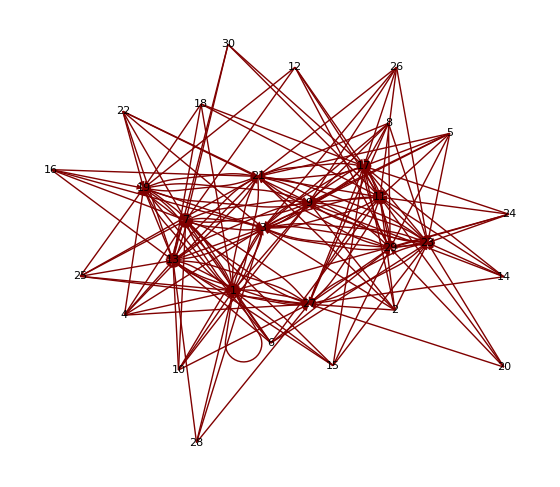

```mathematica
s=Flatten[Outer[List,Range[30],Range[30]],1];
t=DeleteCases[If[PrimeQ[FromDigits[#]],Rule@@#,0]&/@s,0]
GraphPlot[t,VertexLabeling->True,DirectedEdges->True]
```

## 24. Exercise 7.8

```mathematica
Rule@@{a,b}
```

a→b

```mathematica
Rule@@@(Subsequences[{a,b,c,d,e,g,h,j,k},{2}])
```

{a→b,b→c,c→d,d→e,e→g,g→h,h→j,j→k}

```mathematica
Clear[x,i]
```

```mathematica
f[n_]:=Table[x[k]->x[k+1],{k,1,n-1,1}]
f[6]
```

{x[1]→x[2],x[2]→x[3],x[3]→x[4],x[4]→x[5],x[5]→x[6]}

## 25. Exercise 7.9

```mathematica
n=Input["Enter a number: "];
fD[d_]:=FromDigits[Sort[IntegerDigits[d],Greater]]
fA[a_]:=FromDigits[Sort[IntegerDigits[a],Less]]
res[R_]:=fD[R]-fA[R]
Print["You chose: ", n, " L: ",fL[n]," R: ",fR[n]," ",res[n]]
condition[x_]:=(x≠0)&&(x ≠ 6174)
NestWhileList[res[#]&,#,condition[#]&]&[n]
```

You chose: 2323 L: fL[2323] R: fR[2323] 1089

{2323,1089,9621,8352,6174}

```mathematica
n=Range[1000,9999];
res[R_]:=FromDigits[Sort[IntegerDigits[R],Greater]]-FromDigits[Sort[IntegerDigits[R],Less]]
condition[x_]:=x≠0&&x≠6174
masterList=NestWhileList[res/@#&,#,,10]&[n];
```

```mathematica
PositionIndex[Table[Extract[masterList,{j,i}],{i,1,8950},{j,1,10}]]
```

<|{1000,999,0,0,0,0,0,0,0,0}→{1},{1001,1089,9621,8352,6174,6174,6174,6174,6174,6174}→{2},{1002,2088,8532,6174,6174,6174,6174,6174,6174,6174}→{3},8945,{9948,5085,7992,7173,6354,3087,8352,6174,6174,6174}→{8949},{9949,4995,5355,1998,8082,8532,6174,6174,6174,6174}→{8950}|>
 |  |  |  |

```mathematica
PositionIndex[Table[Extract[masterList,{j,i}],{i,1,8950},{j,1,10}]]
```

<|{1000,999,0,0,0,0,0,0,0,0}→{1},{1001,1089,9621,8352,6174,6174,6174,6174,6174,6174}→{2},{1002,2088,8532,6174,6174,6174,6174,6174,6174,6174}→{3},8945,{9948,5085,7992,7173,6354,3087,8352,6174,6174,6174}→{8949},{9949,4995,5355,1998,8082,8532,6174,6174,6174,6174}→{8950}|>
 |  |  |  |

```mathematica
sortable =DeleteDuplicates[Position[Table[Extract[masterList,{j,i}],{i,1,8950},{j,1,10}],6174,2]]
```

{{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},47204,{8946,6},{8946,7},{8946,8},{8946,9},{8946,10},{8947,6},{8947,7},{8947,8},{8947,9},{8947,10},{8948,8},{8948,9},{8948,10},{8949,8},{8949,9},{8949,10},{8950,7},{8950,8},{8950,9},{8950,10}}
 |  |  |  |

```mathematica
(* 1 maximum Iteration is needed to reach 6174. *)
```